## Week 8 - Lecture 7: First Passage Problem - Random Walks

Resources  --  Video  &&  Notes 8g

Check page 3 for basics.
So, an investor wants to understand if a share price will return to the price at which he bought it?
If yes, how long will it take to hit that spot for the first time.
(so that if for example shares have dropped, he can wait to sell it atleast without loss)

#### Number of steps vs Avg fraction of first passage

```mathematica
data = Table[
num=Table[
a={0}; fp=0;
Do[ (* Find if a random walk encountered First Passage *)
AppendTo[a,a[[n-1]] + RandomChoice[{-1,1}]];
If[a[[n]]==0, 
fp=1; Break[]], (* If FP reached, stop the walk *)
{n,2,nsteps}];
fp, {10000}]; (* Repeat for 10k random walks *)
{nsteps, Mean[num]//N}, (* Num steps and fraction of FP *)
{nsteps, {10,50,100,200,500,1000,2000,5000,10000}}];
```

```mathematica
ListPlot[data, Joined->True, PlotMarkers->Automatic]
```

-Graphics-

Hence if the investor waits for a significant time, first passage will definitely occur.

#### Finding the mean time for FP to occur

```mathematica
data = Table[
a={RandomChoice[{-1,1}]}; n=2;
While[n≤10000,
AppendTo[a,a[[n-1]]+ RandomChoice[{-1,1}]];
If[a[[n]] == 0,Break[]];
n++];
n, {10000}];
```

```mathematica
Tally[data // Sort] // TableForm; (* Shows histogram as a table *)
```

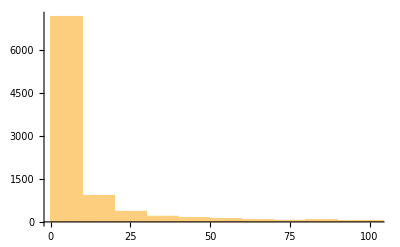

```mathematica
Histogram[data]
```

```mathematica
Mean[data] // N
```

160.541

#### How does the mean time required vary with num. samples?

```mathematica
means=Table[
data = Table[
a={RandomChoice[{-1,1}]}; n=2;
While[n≤20000,
AppendTo[a,a[[n-1]]+ RandomChoice[{-1,1}]];
If[a[[n]] == 0,Break[]];
n++];
n, {nWalks}];
{nWalks, Mean[data]//N}, {nWalks, 100,200,10}];
```

```mathematica
ListPlot[means, Joined->True, PlotMarkers->Automatic]
```

-Graphics-

```mathematica
Mean[means[[;;,2]]]
```

212.939

We see that it has fluctuations.

#### What if we progressively average a single sweep of random walks?

The above method generate many different sweeps, and plotted the average for each sweep.
Here, we try running only 1 sweep, and cumulatively average for time from 1 to t (where t goes from 2 to nWalks).

```mathematica
Take[{1,2,3,4,5,6,7}, 5] (* What is Take[] ? *)
```

{1,2,3,4,5}

```mathematica
data = Table[
a={RandomChoice[{-1,1}]}; n=2;
While[n≤10000,
AppendTo[a,a[[n-1]]+ RandomChoice[{-1,1}]];
If[a[[n]] == 0,Break[]];
n++];
n, {1000}];
```

```mathematica
means=Table[
Mean[Take[data,n]] // N,
{n,1,1000}];
```

```mathematica
ListPlot[means, Joined->True,PlotMarkers->Automatic]
```

-Graphics-

We see that even this does not converge.
Hence, eventhough we can say that first passage will occur, we cannot accurately give a mean value for number of time steps.